```mathematica
link=Install[LinkConnect["39821@192.168.150.128,32839@192.168.150.128",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,ΩO=1/16,Ωe=-100,θr=0.45,θe=Sqrt[0.8],θbp=0.045,θbO=0.01125,ωbp=15*Sqrt[0.7],ωbO=3.75*Sqrt[0.2],ωe=150,
ωp ={0.0292,
0.1255,
0.3348,
0.5943,
0.8157,
0.9857,
1.1176,
1.2200,
1.2972,
1.3513,
1.3833,
1.3939,
1.3833,
1.3513,
1.2972,
1.2200,
1.1176,
0.9857,
0.8157,
0.5943,
0.3348,
0.1255,
0.0292},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd*2.2/2.025,vr*2.2/2.025]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe,ΩO},{ωbp,ωe,ωbO},{θbp,θe,θbO}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
check=With[{k=2.4,wna=88Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.0,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

DispersionKit::warn: wstpDFindRoot - root finder failed at k1 = 0.0984337 and k2 = 1.84738.

{1.93001-0.0652182 ⅈ,1.92142-0.0547565 ⅈ,1.91363-0.0443377 ⅈ,1.9062-0.0333315 ⅈ,1.89963-0.0211593 ⅈ,1.89499-0.00737366 ⅈ,1.89411+0.00772301 ⅈ,1.8986+0.0219305 ⅈ,1.90767+0.0320806 ⅈ,1.91867+0.0366381 ⅈ,1.92888+0.0358954 ⅈ,1.93634+0.0315917 ⅈ,1.94076+0.0261036 ⅈ}

{1.93001-0.0652182 ⅈ,1.92142-0.0547565 ⅈ,1.91363-0.0443377 ⅈ,1.9062-0.0333315 ⅈ,1.89963-0.0211593 ⅈ,1.89499-0.00737366 ⅈ,1.89411+0.00772301 ⅈ,1.8986+0.0219305 ⅈ,1.90767+0.0320806 ⅈ,1.91867+0.0366381 ⅈ,1.92888+0.0358954 ⅈ,1.93634+0.0315917 ⅈ,1.94076+0.0261036 ⅈ,1.94313+0.0208834 ⅈ,1.94441+0.016303 ⅈ,1.94532+0.0123954 ⅈ,1.94615+0.00913512 ⅈ,1.94695+0.00642859 ⅈ,1.94771+0.00428707 ⅈ,1.9484+0.00263439 ⅈ,1.949+0.00139958 ⅈ,1.94949+0.000513432 ⅈ,1.94985-0.0000851368 ⅈ}

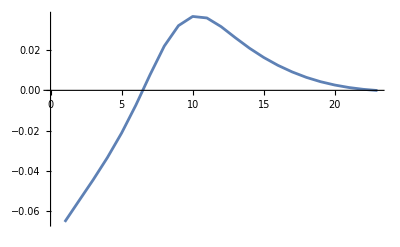

```mathematica
sol1=With[{k=Range[2.5,1.7,-0.05],wna=86.95Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.0,0.03] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol2=With[{k=Range[2.55,3.0,0.05],wna=86.95Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.0,0.03] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol1=Reverse[sol1[[2,2]]]
sol=Join[sol1,sol2[[2,2]]]
ListLinePlot[Im[sol]]
```

```mathematica
Export["vs=2.025,83,0.7h0.2o-0.09-im-2,1.7-3.0.csv",Im[sol]];

Export["vs=2.025,83,0.7h0.2o-0.09-re-2,1.7-3.0.csv",Re[sol]];
```